# Relativist Quantum Mechanics Workshop II

## Author: León Ocaña

From the following equations





compute



where




Solution:

```mathematica
Subscript[ψ, 1][x_]=A ⅇ^(k1 x)
Subscript[ψ, 2][x_]=c ⅇ^(ⅈ k2 x) + d ⅇ^(-ⅈ k2 x)
Subscript[ψ, 3][x_]=G ⅇ^(-k1 x)
```

A ⅇ^(k1 x)

d ⅇ^(-ⅈ k2 x)+c ⅇ^(ⅈ k2 x)

ⅇ^(-k1 x) G

1.- Getting Boundary conditions

```mathematica
FirstBC = Subscript[ψ, 1][-a]==Subscript[ψ, 2][-a]
```

A ⅇ^(-a k1)==c ⅇ^(-ⅈ a k2)+d ⅇ^(ⅈ a k2)

```mathematica
SecondBC = Subscript[ψ, 1]'[-a]==Subscript[ψ, 2]'[-a]
```

A ⅇ^(-a k1) k1==ⅈ c ⅇ^(-ⅈ a k2) k2-ⅈ d ⅇ^(ⅈ a k2) k2

```mathematica
ThirdBC = Subscript[ψ, 3][a]==Subscript[ψ, 2][a]
```

ⅇ^(-a k1) G==d ⅇ^(-ⅈ a k2)+c ⅇ^(ⅈ a k2)

```mathematica
FourthBC = Subscript[ψ, 3]'[a]==Subscript[ψ, 2]'[a]
```

-ⅇ^(-a k1) G k1==-ⅈ d ⅇ^(-ⅈ a k2) k2+ⅈ c ⅇ^(ⅈ a k2) k2

2.- Sum the first and third equations

```mathematica
Sum1and3 = FullSimplify[(FirstBC[[1]]+ThirdBC[[1]])]==FullSimplify[(FirstBC[[2]]+ThirdBC[[2]])]
```

ⅇ^(-a k1) (A+G)==2 (c+d) Cos[a k2]

3.- Substract the second and fourth equations

```mathematica
Substract2and4 = FullSimplify[(SecondBC[[1]]-FourthBC[[1]])]==FullSimplify[(SecondBC[[2]]-FourthBC[[2]])]
```

ⅇ^(-a k1) (A+G) k1==2 (c+d) k2 Sin[a k2]

Dividing “Substract2and4” by “Sum1and3”

```mathematica
division = FullSimplify[Substract2and4[[1]]/Sum1and3[[1]] ]== FullSimplify[Substract2and4[[2]]/Sum1and3[[2]]]
```

k1==k2 Tan[a k2]

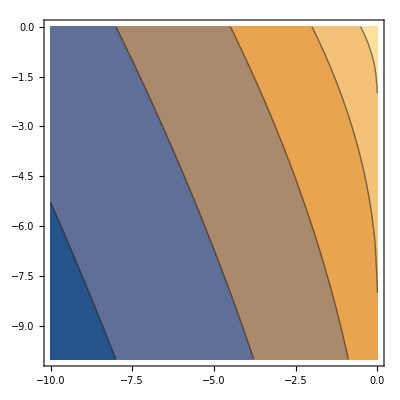

```mathematica
ContourPlot[-(√(-2 e))+(√(2(e+v0)))Tan[a (√(2(e+v0)))]/.a->2,{e,-10,0},{v0,-10,0}]
```